## Model described in Reluga, Dahari, Perelson 2009 [1]

[1] Reluga, T. C., Dahari, H., & Perelson, A. S. (2009). Analysis of hepatitis C virus infection models with hepatocyte homeostasis. SIAM Journal on Applied Mathematics, 69(4), 999-1023.

### Data for the left plot in figure 2

```mathematica
s=0;
rT=3;
Tmax=5000000;
dT=0.012;
eta=0;
beta =0.0000014;
q=0.0;
rI=0.97;
dI=0.36;
c=6.0;
p=28.7;
epsil=0.98;
```

### Data for the right plot in figure 2

{{T→InterpolatingFunction[{{0., 100.}}, <>],IN→InterpolatingFunction[{{0., 100.}}, <>],VIR→InterpolatingFunction[{{0., 100.}}, <>]}}

{1.6×10^7,1.94236×10^6,143186.,77806.9,62892.8,61122.2,59409.1,57067.3,54674.8,51475.1,40513.6,25803.4,18363.1,11582.9,4877.23}

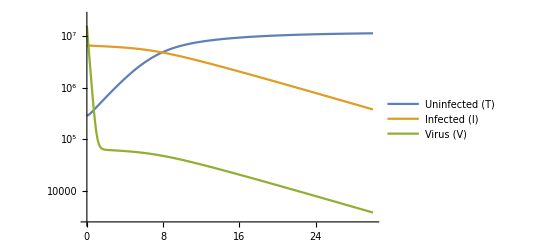

```mathematica
s=0;
rT=1.1;
Tmax=1.2*^7;
dT=0.012;
eta=0;
beta = 2.8*^-8;
q=0.0;
rI=0.26;
dI=0.13;
c=5.4;
p=13.2;
epsil=0.996;
sol=NDSolve[{T'[t]==s+rT T[t](1-(T[t]+IN[t])/Tmax)-dT T[t]-(1-eta) beta VIR[t] T[t]+q IN[t],
IN'[t]==rI IN[t](1-(T[t]+IN[t])/Tmax)-dI IN[t]+(1-eta) beta VIR[t] T[t]-q IN[t],
VIR'[t]==(1-epsil)p IN[t] - c VIR[t],T[0]==2.9*^5,IN[0]==6.61*^6,VIR[0]==1.6*^7},
{T,IN,VIR},
{t,0,100}]
RNA[t_] = VIR[t]/.sol[[1]][[3]];


RNA/@{0,0.396,0.982,1.2988,1.9958,2.9937,3.9916,5.0845,5.9873,7.0011,9.8838,14.0813,17.0116,20.8765,27.9884}
LogPlot[Evaluate[{T[t], IN[t], VIR[t]} /. sol], {t, 0,30}, PlotStyle->Automatic, PlotLegends->{"Uninfected (T)", "Infected (I)", "Virus (V)"}, PlotTheme->"Bussines"]
```